# Berechnung der effektiven Geschwindigkeit bei M=0

```mathematica
σx=τx=PauliMatrix[1];
σy=τy=PauliMatrix[2];
σz=τz=PauliMatrix[3];
σ0=τ0=IdentityMatrix[2];
σ0τ0=KroneckerProduct[τ0,σ0];
σxτz=KroneckerProduct[τz,σx];
σyτz=KroneckerProduct[τz,σy];
σxτy=KroneckerProduct[τy,σx];
σyτy=KroneckerProduct[τy,σy];
σzτy=KroneckerProduct[τy,σz];
τx11=KroneckerProduct[τx,σ0];
τy11=KroneckerProduct[τy,σ0];
τz11=KroneckerProduct[τz,σ0];
```

```mathematica
$Assumptions=ℏ>=0&&v>=0&&μ∈Reals&&ℏ∈Reals&&v∈Reals;
```

```mathematica
h0=FullSimplify[-ℏ*v*I*dx*σxτz-μ*τz11+Δ*(τx11*Cos[ϕ]+τy11*Sin[ϕ])];
h1=-ℏ*v*I *dy*σyτz;
h=h0+h1;
MatrixForm[h]
```

(-μ | -ⅈ dx v ℏ-dy v ℏ | ⅇ^(-ⅈ ϕ) Δ | 0
-ⅈ dx v ℏ+dy v ℏ | -μ | 0 | ⅇ^(-ⅈ ϕ) Δ
ⅇ^(ⅈ ϕ) Δ | 0 | μ | ⅈ dx v ℏ+dy v ℏ
0 | ⅇ^(ⅈ ϕ) Δ | ⅈ dx v ℏ-dy v ℏ | μ)

```mathematica
$Assumptions=ℏ>0&&v>0&&Δ>0&&L>0 &&            μ∈Reals&&ℏ∈Reals&&v∈Reals&&x∈Reals&&ϵ∈Reals&&μ∈Reals&&ϕ∈Reals&&Δ∈Reals&&ϵ1∈Reals&&ϵ2∈Reals&&ϵ3∈Reals&&ϵ4∈Reals&&L∈Reals&&     ϵ<Δ  &&    Re[Sqrt[ ϵ^2-Δ^2]]==0 && Conjugate[√(-Δ^2+ϵ^2)]==I √(Δ^2-ϵ^2);
```

Heaviside-Funktionen für einzelnen Wellenfunktionen in den Teilbereichen:

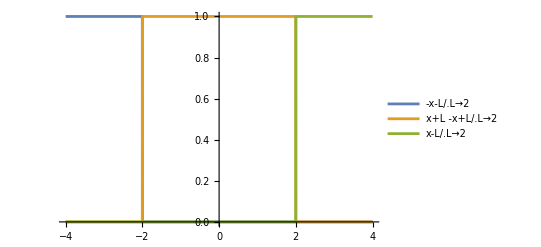

```mathematica
Plot[{
HeavisideTheta[-x-L]                                                                      /.L->2,
HeavisideTheta[x+L] HeavisideTheta[-x+L]                       /.L->2,
HeavisideTheta[x-L]                                                                        /.L->2
},{x,-4,4},PlotLegends->"Expressions"]
```

## Wellenfunktionen zusammengesetzt aus vorherigen Mathematica-Notebooks

Von Hand ersetzen:       {a, b, Theta}; σ2 bekommt ϵ-> -ϵ. ϕ wird später ersetzt durch den arccos (in beiden gleich), ϕ ist reel

```mathematica
σ1=FullSimplify[((({{-(ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, 0, ⅇ^((ⅈ x (ϵ+μ))/(v ℏ)), -ⅇ^(-(ⅈ x (ϵ+μ))/(v ℏ)), 0, (ⅇ^(-ⅈ ϕ+(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-ⅈ ϕ+(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ}, {(ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, 0, ⅇ^((ⅈ x (ϵ+μ))/(v ℏ)), ⅇ^(-(ⅈ x (ϵ+μ))/(v ℏ)), 0, (ⅇ^(-ⅈ ϕ+(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-ⅈ ϕ+(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ}, {-ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)), ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), -ⅇ^((ⅈ x (ϵ-μ))/(v ℏ)), 0, 0, ⅇ^(-(ⅈ x (ϵ-μ))/(v ℏ)), -ⅇ^((ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^((ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ))}, {ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)), ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^((ⅈ x (ϵ-μ))/(v ℏ)), 0, 0, ⅇ^(-(ⅈ x (ϵ-μ))/(v ℏ)), ⅇ^((ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^((ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ))}}).({{0}, {HeavisideTheta[-x-L]}, {0}, {-(ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)))/Δ HeavisideTheta[x+L] HeavisideTheta[-x+L]}, {0}, {ⅇ^((ⅈ L (-ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[x+L] HeavisideTheta[-x+L]}, {0}, {- (ⅇ^(ⅈ ϕ) ⅇ^(ⅈ (2 L ϵ)/(v ℏ))(Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))))/Δ^2 HeavisideTheta[x-L]}})))];
σ2=FullSimplify[((({{-(ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, 0, ⅇ^((ⅈ x (ϵ+μ))/(v ℏ)), -ⅇ^(-(ⅈ x (ϵ+μ))/(v ℏ)), 0, (ⅇ^(-ⅈ ϕ+(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-ⅈ ϕ+(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ}, {(ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, 0, ⅇ^((ⅈ x (ϵ+μ))/(v ℏ)), ⅇ^(-(ⅈ x (ϵ+μ))/(v ℏ)), 0, (ⅇ^(-ⅈ ϕ+(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-ⅈ ϕ+(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ}, {-ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)), ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), -ⅇ^((ⅈ x (ϵ-μ))/(v ℏ)), 0, 0, ⅇ^(-(ⅈ x (ϵ-μ))/(v ℏ)), -ⅇ^((ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^((ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ))}, {ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)), ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^((ⅈ x (ϵ-μ))/(v ℏ)), 0, 0, ⅇ^(-(ⅈ x (ϵ-μ))/(v ℏ)), ⅇ^((ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^((ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ))}}).({{HeavisideTheta[-x-L]}, {0}, {ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ))HeavisideTheta[x+L] HeavisideTheta[-x+L]}, {0}, {(ⅇ^((ⅈ L (-ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ HeavisideTheta[x+L] HeavisideTheta[-x+L]}, {0}, {(ⅇ^(ⅈ ϕ) ⅇ^(-ⅈ (2 L ϵ)/(v ℏ))(-Δ^2+2 ϵ (ϵ+√(-Δ^2+ϵ^2))))/Δ^2 HeavisideTheta[x-L]}, {0}})))/.ϵ->-ϵ];
```

```mathematica
MatrixForm[σ1]
MatrixForm[σ2]
```

(-(ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)) (HeavisideTheta[-L-x]+ⅇ^((2 ⅈ (L ϵ+x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L+x) (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]))/Δ
-(ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)) (HeavisideTheta[-L-x]+ⅇ^((2 ⅈ (L ϵ+x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L+x) (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]))/Δ
ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) HeavisideTheta[-L-x]-(ⅇ^((ⅈ (2 L ϵ+x (√(-Δ^2+ϵ^2)+μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x])/Δ^2+ⅇ^((ⅈ (-((L+x) ϵ)+L √(-Δ^2+ϵ^2)+x μ))/(v ℏ)) HeavisideTheta[L-x,L+x]
ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) HeavisideTheta[-L-x]-(ⅇ^((ⅈ (2 L ϵ+x (√(-Δ^2+ϵ^2)+μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x])/Δ^2+ⅇ^((ⅈ (-((L+x) ϵ)+L √(-Δ^2+ϵ^2)+x μ))/(v ℏ)) HeavisideTheta[L-x,L+x])

(-(ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)) (HeavisideTheta[-L-x]+ⅇ^((2 ⅈ (L ϵ+x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L+x) (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]))/Δ
(ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)) (HeavisideTheta[-L-x]+ⅇ^((2 ⅈ (L ϵ+x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L+x) (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]))/Δ
-ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) HeavisideTheta[-L-x]+(ⅇ^((ⅈ (2 L ϵ+x (√(-Δ^2+ϵ^2)-μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x])/Δ^2-ⅇ^((ⅈ (L (-ϵ+√(-Δ^2+ϵ^2))-x (ϵ+μ)))/(v ℏ)) HeavisideTheta[L-x,L+x]
ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) HeavisideTheta[-L-x]-(ⅇ^((ⅈ (2 L ϵ+x (√(-Δ^2+ϵ^2)-μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x])/Δ^2+ⅇ^((ⅈ (L (-ϵ+√(-Δ^2+ϵ^2))-x (ϵ+μ)))/(v ℏ)) HeavisideTheta[L-x,L+x])

Konjugiere von Hand:

```mathematica
σ1Conj=({{-(ⅇ^(-(-ⅈ x (-√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (-ϵ-√(-Δ^2+ϵ^2)) (HeavisideTheta[-L-x]+ⅇ^((-2 ⅈ (L ϵ-x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((-ⅈ (L+x) (ϵ-√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]))/Δ}, {-(ⅇ^(-(-ⅈ x (-√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (-ϵ-√(-Δ^2+ϵ^2)) (HeavisideTheta[-L-x]+ⅇ^((-2 ⅈ (L ϵ-x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((-ⅈ (L+x) (ϵ-√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]))/Δ}, {ⅇ^(-(-ⅈ x (-√(-Δ^2+ϵ^2)-μ))/(v ℏ)) HeavisideTheta[-L-x]-(ⅇ^((-ⅈ (2 L ϵ+x (-√(-Δ^2+ϵ^2)+μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ-√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x])/Δ^2+ⅇ^((-ⅈ (-((L+x) ϵ)-L √(-Δ^2+ϵ^2)+x μ))/(v ℏ)) HeavisideTheta[L-x,L+x]}, {ⅇ^(-(-ⅈ x (-√(-Δ^2+ϵ^2)-μ))/(v ℏ)) HeavisideTheta[-L-x]-(ⅇ^((-ⅈ (2 L ϵ+x (-√(-Δ^2+ϵ^2)+μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ-√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x])/Δ^2+ⅇ^((-ⅈ (-((L+x) ϵ)-L √(-Δ^2+ϵ^2)+x μ))/(v ℏ)) HeavisideTheta[L-x,L+x]}});
σ2Conj=({{-(ⅇ^(-(-ⅈ x (-√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (-ϵ-√(-Δ^2+ϵ^2)) (HeavisideTheta[-L-x]+ⅇ^((-2 ⅈ (L ϵ-x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((-ⅈ (L+x) (ϵ-√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]))/Δ}, {(ⅇ^(-(-ⅈ x (-√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (-ϵ-√(-Δ^2+ϵ^2)) (HeavisideTheta[-L-x]+ⅇ^((-2 ⅈ (L ϵ-x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((-ⅈ (L+x) (ϵ-√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]))/Δ}, {-ⅇ^(-(-ⅈ x (-√(-Δ^2+ϵ^2)+μ))/(v ℏ)) HeavisideTheta[-L-x]+(ⅇ^((-ⅈ (2 L ϵ+x (-√(-Δ^2+ϵ^2)-μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ-√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x])/Δ^2-ⅇ^((-ⅈ (L (-ϵ-√(-Δ^2+ϵ^2))-x (ϵ+μ)))/(v ℏ)) HeavisideTheta[L-x,L+x]}, {ⅇ^(-(-ⅈ x (-√(-Δ^2+ϵ^2)+μ))/(v ℏ)) HeavisideTheta[-L-x]-(ⅇ^((-ⅈ (2 L ϵ+x (-√(-Δ^2+ϵ^2)-μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ-√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x])/Δ^2+ⅇ^((-ⅈ (L (-ϵ-√(-Δ^2+ϵ^2))-x (ϵ+μ)))/(v ℏ)) HeavisideTheta[L-x,L+x]}});
```

Wellenfunktionen normieren (numerisch):

```mathematica
NNormIntegral1=NIntegrate[(σ1Conj.σ1/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},{x,-50,50}]
NNormFactor1=Sqrt[Re[1/NNormIntegral1]]
NNormIntegral2=NIntegrate[(σ2Conj.σ2/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},{x,-50,50}]
NNormFactor2=Sqrt[Re[1/NNormIntegral2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.07344}. NIntegrate obtained 1.64316+0. ⅈ and 0.0000633097 for the integral and error estimates.

1.64316+0. ⅈ

0.780119

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.07344}. NIntegrate obtained 1.64316+0. ⅈ and 0.0000633097 for the integral and error estimates.

1.64316+0. ⅈ

0.780119

```mathematica
Nσ1=NNormFactor1*σ1;
Nσ2=NNormFactor2*σ2;
Nσ1Conj=NNormFactor1*σ1Conj;
Nσ2Conj=NNormFactor2*σ2Conj;
```

Normierung überprüfen:

```mathematica
NIntegrate[(Nσ1Conj.Nσ1/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},{x,-50,50}]
NIntegrate[(Nσ2Conj.Nσ2/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},{x,-50,50}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.07344}. NIntegrate obtained 1.-1.42346×10^-18 ⅈ and 0.0000385293 for the integral and error estimates.

1.-1.42346×10^-18 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.07344}. NIntegrate obtained 1.-3.7748×10^-19 ⅈ and 0.0000385293 for the integral and error estimates.

1.-3.7748×10^-19 ⅈ

Normierung der Wellenfunktion (analytisch):

```mathematica
productNorm1=Simplify[σ1Conj.σ1/.√(-Δ^2+ϵ^2)->I √(Δ^2-ϵ^2)];
NormIntegral1=Integrate[productNorm1,{x,-Infinity,Infinity}]
productNorm2=Simplify[σ2Conj.σ2/.√(-Δ^2+ϵ^2)->I √(Δ^2-ϵ^2)];
NormIntegral2=Integrate[productNorm1,{x,-Infinity,Infinity}]
```

(4 ⅇ^(-(2 L √(Δ^2-ϵ^2))/(v ℏ)) (2 L √(Δ^2-ϵ^2)+v ℏ))/(√(Δ^2-ϵ^2))

(4 ⅇ^(-(2 L √(Δ^2-ϵ^2))/(v ℏ)) (2 L √(Δ^2-ϵ^2)+v ℏ))/(√(Δ^2-ϵ^2))

```mathematica
NormFactor1=1/Sqrt[NormIntegral1]
NormFactor2=1/Sqrt[NormIntegral2]
σ1=NormFactor1*σ1;
σ2=NormFactor2*σ2;
σ1Conj=NormFactor1*σ1Conj;
σ2Conj=NormFactor2*σ2Conj;
```

1/(2 √((ⅇ^(-(2 L √(Δ^2-ϵ^2))/(v ℏ)) (2 L √(Δ^2-ϵ^2)+v ℏ))/(√(Δ^2-ϵ^2))))

1/(2 √((ⅇ^(-(2 L √(Δ^2-ϵ^2))/(v ℏ)) (2 L √(Δ^2-ϵ^2)+v ℏ))/(√(Δ^2-ϵ^2))))

```mathematica
productNorm1=Simplify[σ1Conj.σ1/.√(-Δ^2+ϵ^2)->I √(Δ^2-ϵ^2)];
(*productNorm2=Simplify[σ2Conj.σ2/.√(-Δ^2+ϵ^2)->I √(Δ^2-ϵ^2)];*)
Integrate[productNorm1,{x,-Infinity,Infinity}]
(*Integrate[productNorm2,{x,-Infinity,Infinity}]*)
```

1

Plotten der Wellenfunktionen:
1. Numerische Normierung (Plot):

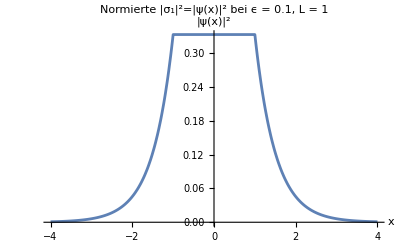

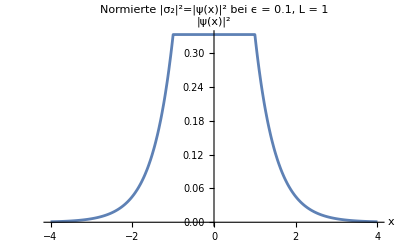

```mathematica
Plot[(Nσ1Conj.Nσ1/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},{x,-4,4},AxesLabel->{"x","|ψ(x)|^2"},PlotLabel->"Normierte |σ_1|^2=|ψ(x)|^2 bei ϵ = 0.1, L = 1"]
Plot[(Nσ2Conj.Nσ2 /.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},{x,-4,4},AxesLabel->{"x","|ψ(x)|^2"},PlotLabel->"Normierte |σ_2|^2=|ψ(x)|^2 bei ϵ = 0.1, L = 1"]
```

2. Analytische Normierung (Plot):

```mathematica
Plot[(σ1Conj.σ1/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},{x,-4,4},AxesLabel->{"x","|ψ(x)|^2"},PlotLabel->"Normierte |σ_1|^2=|ψ(x)|^2 bei ϵ = 0.1, L = 1"]
Plot[(σ2Conj.σ2 /.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},{x,-4,4},AxesLabel->{"x","|ψ(x)|^2"},PlotLabel->"Normierte |σ_2|^2=|ψ(x)|^2 bei ϵ = 0.1, L = 1"]
```

-Graphics-

-Graphics-

Matrixelemente numerisch berechnen:

```mathematica
Nσ1σ1=Simplify[(Nσ1Conj.σyτz.Nσ1/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1}]
Nσ1σ2=Simplify[(Nσ1Conj.σyτz.Nσ2/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1}]
Nσ2σ1=Simplify[(Nσ2Conj.σyτz.Nσ1/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1}]
Nσ2σ2=Simplify[(Nσ2Conj.σyτz.Nσ2/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1}]
```

0.+0. ⅈ

ⅇ^((-3.97995-6.1 ⅈ) x) ((0.+2.43434 ⅈ) ⅇ^((5.96992+4.1 ⅈ) x) HeavisideTheta[-1-x]^2-(6.75665×10^-17-2.43434 ⅈ) ⅇ^((1.98997+4.1 ⅈ) x) HeavisideTheta[-1+x]^2+ⅇ^(2.98496 x) ((-0.0898545+0.895548 ⅈ) ⅇ^((0.+4. ⅈ) x)+(0.0898545+0.895548 ⅈ) ⅇ^((0.+4.2 ⅈ) x)) HeavisideTheta[-1+x] HeavisideTheta[1-x,1+x]-(7.70372×10^-34-0.332772 ⅈ) ⅇ^((3.97995+4.1 ⅈ) x) HeavisideTheta[1-x,1+x]^2+HeavisideTheta[-1-x] ((-6.75665×10^-17+4.77163 ⅈ) ⅇ^((3.97995+4.1 ⅈ) x) HeavisideTheta[-1+x]+ⅇ^(4.97494 x) ((0.0898545+0.895548 ⅈ) ⅇ^((0.+4. ⅈ) x)-(0.0898545-0.895548 ⅈ) ⅇ^((0.+4.2 ⅈ) x)) HeavisideTheta[1-x,1+x]))

ⅇ^((-3.97995-0.1 ⅈ) x) ((1.2326×10^-32-2.43434 ⅈ) ⅇ^((5.96992+2.1 ⅈ) x) HeavisideTheta[-1-x]^2+(6.75665×10^-17-2.43434 ⅈ) ⅇ^((1.98997+2.1 ⅈ) x) HeavisideTheta[-1+x]^2+ⅇ^(2.98496 x) ((0.0898545-0.895548 ⅈ) ⅇ^((0.+2. ⅈ) x)-(0.0898545+0.895548 ⅈ) ⅇ^((0.+2.2 ⅈ) x)) HeavisideTheta[-1+x] HeavisideTheta[1-x,1+x]-(7.70372×10^-34+0.332772 ⅈ) ⅇ^((3.97995+2.1 ⅈ) x) HeavisideTheta[1-x,1+x]^2+HeavisideTheta[-1-x] ((6.75665×10^-17-4.77163 ⅈ) ⅇ^((3.97995+2.1 ⅈ) x) HeavisideTheta[-1+x]+ⅇ^(4.97494 x) ((-0.0898545-0.895548 ⅈ) ⅇ^((0.+2. ⅈ) x)+(0.0898545-0.895548 ⅈ) ⅇ^((0.+2.2 ⅈ) x)) HeavisideTheta[1-x,1+x]))

0.

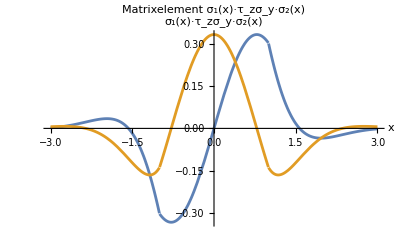

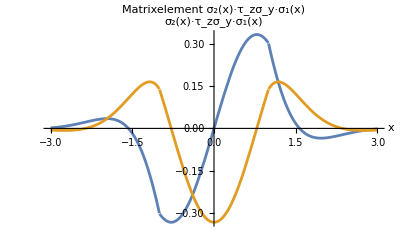

```mathematica
Plot[{Re[Nσ1σ2],Im[Nσ1σ2]},{x,-3,3},PlotRange->Full,PlotLabel->"Matrixelement σ_1(x)·τ_zσ_y·σ_2(x)",AxesLabel->{"x","σ_1(x)·τ_zσ_y·σ_2(x)"}]
Plot[{Re[Nσ2σ1],Im[Nσ2σ1]},{x,-3,3},PlotRange->Full,PlotLabel->"Matrixelement σ_2(x)·τ_zσ_y·σ_1(x)",AxesLabel->{"x","σ_2(x)·τ_zσ_y·σ_1(x)"}]
```

```mathematica
NIntegrate[Nσ1σ2,{x,-0.8,0.8}]
NIntegrate[Nσ1σ2,{x,-2,2}]
NIntegrate[Nσ1σ2,{x,-10,10}]
NmatrixElement12=NIntegrate[Nσ1σ2,{x,-100,100}]
```

-1.38778×10^-17+0.33263 ⅈ

2.77556×10^-17+0.0788609 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.996249}. NIntegrate obtained 4.84503×10^-17+0.0812939 ⅈ and 1.86057×10^-6 for the integral and error estimates.

4.84503×10^-17+0.0812939 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.988867}. NIntegrate obtained 1.3007×10^-17+0.0812939 ⅈ and 1.79878×10^-7 for the integral and error estimates.

1.3007×10^-17+0.0812939 ⅈ

```mathematica
NIntegrate[Nσ2σ1,{x,-0.8,0.8}]
NIntegrate[Nσ2σ1,{x,-2,2}]
NIntegrate[Nσ2σ1,{x,-10,10}]
NmatrixElement21=NIntegrate[Nσ2σ1,{x,-100,100}]
```

8.67362×10^-19-0.33263 ⅈ

6.245×10^-17-0.0788609 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.996249}. NIntegrate obtained -2.51535×10^-17-0.0812938 ⅈ and 2.3134×10^-6 for the integral and error estimates.

-2.51535×10^-17-0.0812938 ⅈ

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.025}. NIntegrate obtained 6.93889×10^-17-0.0812932 ⅈ and 0.0000138349 for the integral and error estimates.

6.93889×10^-17-0.0812932 ⅈ

```mathematica
Nρ={{Nσ1σ1,NmatrixElement12},{NmatrixElement21,Nσ2σ2}};
MatrixForm[Nρ]
NρRounded={{Round[Re[Nσ1σ1]],N[Round[Im[NmatrixElement12]*10000]/10000]I},{N[Round[Im[NmatrixElement21]*10000]/10000]I,Round[Nσ2σ2]}};
MatrixForm[NρRounded]
```

(0.+0. ⅈ | 1.3007×10^-17+0.0812939 ⅈ
6.93889×10^-17-0.0812932 ⅈ | 0.)

(0 | 0.+0.0813 ⅈ
0.-0.0813 ⅈ | 0)

Matrixelemente analytisch berechnen:

```mathematica
σ1σ1=FullSimplify[Conjugate[σ1].σyτz.σ1]
σ1σ2=Simplify[σ1Conj.σyτz.σ2]
σ2σ1=Simplify[σ2Conj.σyτz.σ1]
σ2σ2=FullSimplify[Conjugate[σ2].σyτz.σ2]
```

0

1/(4 (2 L √(Δ^2-ϵ^2)+v ℏ))ⅈ ⅇ^((2 L √(Δ^2-ϵ^2))/(v ℏ)) √(Δ^2-ϵ^2) (2 ⅇ^(-(ⅈ (2 L ϵ+x (ϵ+2 (√(-Δ^2+ϵ^2)+μ))))/(v ℏ)) (HeavisideTheta[-L-x]+ⅇ^((2 ⅈ (L ϵ+x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L+x) (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]) (ⅇ^((ⅈ (2 L+x) ϵ)/(v ℏ)) HeavisideTheta[-L-x]+ⅇ^((ⅈ x (ϵ+2 √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((ⅈ (x √(-Δ^2+ϵ^2)+L (ϵ+√(-Δ^2+ϵ^2))))/(v ℏ)) HeavisideTheta[L-x,L+x])+1/Δ^4 2 (ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) Δ^2 HeavisideTheta[-L-x]+ⅇ^(-(ⅈ (2 L ϵ+x (-√(-Δ^2+ϵ^2)+μ)+v ϕ ℏ))/(v ℏ)) (-Δ^2+2 ϵ (ϵ+√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L (ϵ+√(-Δ^2+ϵ^2))+x (ϵ-μ)))/(v ℏ)) Δ^2 HeavisideTheta[L-x,L+x]) (ⅇ^(-(ⅈ x (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) Δ^2 HeavisideTheta[-L-x]-ⅇ^((ⅈ (2 L ϵ+x (√(-Δ^2+ϵ^2)-μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L (-ϵ+√(-Δ^2+ϵ^2))-x (ϵ+μ)))/(v ℏ)) Δ^2 HeavisideTheta[L-x,L+x]))

-1/(4 (2 L √(Δ^2-ϵ^2)+v ℏ))ⅈ ⅇ^((2 L √(Δ^2-ϵ^2))/(v ℏ)) √(Δ^2-ϵ^2) (2 ⅇ^(-(ⅈ (2 L ϵ+x (ϵ+√(-Δ^2+ϵ^2)-2 μ)))/(v ℏ)) (ⅇ^((ⅈ (2 L ϵ+x (ϵ-√(-Δ^2+ϵ^2))))/(v ℏ)) HeavisideTheta[-L-x]+ⅇ^((ⅈ x (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x]) (HeavisideTheta[-L-x]+ⅇ^((2 ⅈ (L ϵ+x √(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L+x) (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) HeavisideTheta[L-x,L+x])+1/Δ^4 2 ⅇ^(-(ⅈ (L+x) ϵ)/(v ℏ)) (ⅇ^((ⅈ (L ϵ+x (ϵ-√(-Δ^2+ϵ^2)+μ)))/(v ℏ)) Δ^2 HeavisideTheta[-L-x]-ⅇ^((ⅈ (3 L ϵ+x (ϵ+√(-Δ^2+ϵ^2)+μ)+v ϕ ℏ))/(v ℏ)) (Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L √(-Δ^2+ϵ^2)+x μ))/(v ℏ)) Δ^2 HeavisideTheta[L-x,L+x]) (ⅇ^((ⅈ x (-√(-Δ^2+ϵ^2)+μ))/(v ℏ)) Δ^2 HeavisideTheta[-L-x]+ⅇ^(-(ⅈ (2 L ϵ-x (√(-Δ^2+ϵ^2)+μ)+v ϕ ℏ))/(v ℏ)) (-Δ^2+2 ϵ (ϵ+√(-Δ^2+ϵ^2))) HeavisideTheta[-L+x]+ⅇ^((ⅈ (L (ϵ+√(-Δ^2+ϵ^2))+x (ϵ+μ)))/(v ℏ)) Δ^2 HeavisideTheta[L-x,L+x]))

0

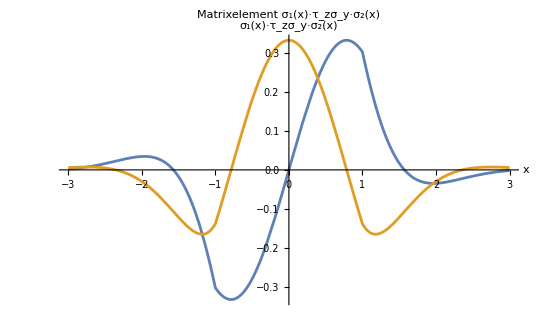

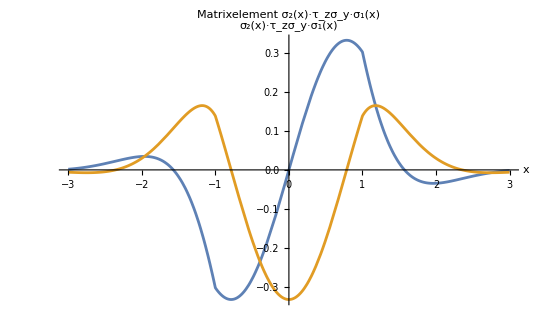

```mathematica
Plot[{(Re[σ1σ2]/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},(Im[σ1σ2]/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1}},{x,-3,3},PlotRange->Full,PlotLabel->"Matrixelement σ_1(x)·τ_zσ_y·σ_2(x)",AxesLabel->{"x","σ_1(x)·τ_zσ_y·σ_2(x)"}]
Plot[{(Re[σ2σ1]/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1},(Im[σ2σ1]/.ϕ->ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1}},{x,-3,3},PlotRange->Full,PlotLabel->"Matrixelement σ_2(x)·τ_zσ_y·σ_1(x)",AxesLabel->{"x","σ_2(x)·τ_zσ_y·σ_1(x)"}]
(*, PlotLabels->"Expressions"*)
```

```mathematica
MatrixElement12=Integrate[σ1σ2,{x,-Infinity,Infinity}]
MatrixElement21=Integrate[σ2σ1,{x,-Infinity,Infinity}]
```

-(ⅇ^((2 L (√(Δ^2-ϵ^2)+ⅈ √(-Δ^2+ϵ^2)-ⅈ μ))/(v ℏ)) v √(Δ^2-ϵ^2) ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) Δ^2-(-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) ϵ^2+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 (√(-Δ^2+ϵ^2)-μ) μ (√(-Δ^2+ϵ^2)+μ) (2 L √(Δ^2-ϵ^2)+v ℏ))

(ⅇ^((2 L (√(Δ^2-ϵ^2)+ⅈ √(-Δ^2+ϵ^2)-ⅈ μ))/(v ℏ)) v √(Δ^2-ϵ^2) ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) Δ^2-(-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) ϵ^2+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 (√(-Δ^2+ϵ^2)-μ) μ (√(-Δ^2+ϵ^2)+μ) (2 L √(Δ^2-ϵ^2)+v ℏ))

```mathematica
MatrixElement12/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1}
MatrixElement21/.{L->1,v->1,ϵ->0.1,Δ->1,ℏ->1,μ->1}
```

3.46945×10^-18+0.0812946 ⅈ

-3.46945×10^-18-0.0812946 ⅈ

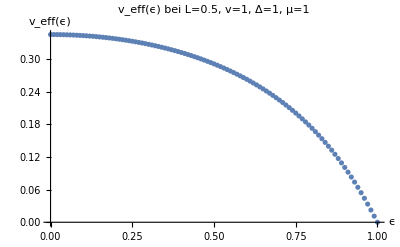

```mathematica
replaceValues={L->0.5,v->1,Δ->1,ℏ->1,μ->1};
veffPlotPoints01=Table[{ϵ,Im[MatrixElement12/.replaceValues]},{ϵ,0,1,0.01}];
ListPlot[veffPlotPoints01,PlotLabel->"v_eff(ϵ) bei L=0.5, v=1, Δ=1, μ=1",AxesLabel->{"ϵ","v_eff(ϵ)"}]
```

Analytische Umformung der Matrixelemente:

analytische Lösung umformen:

```mathematica
(ⅇ^((2 L (√(Δ^2-ϵ^2)+ⅈ √(-Δ^2+ϵ^2)-ⅈ μ))/(v ℏ)) v √(Δ^2-ϵ^2) ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) Δ^2-(-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) ϵ^2+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 (√(-Δ^2+ϵ^2)-μ) μ (√(-Δ^2+ϵ^2)+μ) (2 L √(Δ^2-ϵ^2)+v ℏ))
=(ⅇ^((2 L (√(Δ^2-ϵ^2)- √(Δ^2-ϵ^2)-ⅈ μ))/(v ℏ)) v √(Δ^2-ϵ^2) ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) Δ^2-(-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) ϵ^2+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 (√(-Δ^2+ϵ^2)-μ) μ (√(-Δ^2+ϵ^2)+μ) (2 L √(Δ^2-ϵ^2)+v ℏ))
=(ⅇ^((-2 L ⅈ μ)/(v ℏ)) v √(Δ^2-ϵ^2) ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) Δ^2-(-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) ϵ^2+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 (√(-Δ^2+ϵ^2)-μ) μ (√(-Δ^2+ϵ^2)+μ) (2 L √(Δ^2-ϵ^2)+v ℏ))
=(ⅇ^((-2 L ⅈ μ)/(v ℏ)) v √(Δ^2-ϵ^2) ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) Δ^2-(-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) ϵ^2+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 (-(√(Δ^2-ϵ^2))^2-μ^2) μ  (2 L √(Δ^2-ϵ^2)+v ℏ))
=(ⅇ^((-2 L ⅈ μ)/(v ℏ)) v √(Δ^2-ϵ^2) ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) Δ^2-(-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) ϵ^2+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 μ(-(√(Δ^2-ϵ^2))^2*2 L √(Δ^2-ϵ^2)-v ℏ(√(Δ^2-ϵ^2))^2-μ^2*2 L √(Δ^2-ϵ^2)-μ*v ℏ))
=(ⅇ^((-2 L ⅈ μ)/(v ℏ)) v  ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) Δ^2-(-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) ϵ^2+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 μ(-(√(Δ^2-ϵ^2))^2*2 L -v ℏ √(Δ^2-ϵ^2)-μ^2*2 L -(μv ℏ)/(√(Δ^2-ϵ^2))))
=(ⅇ^((-2 L ⅈ μ)/(v ℏ)) v  ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) (Δ^2-ϵ^2)+(1+ⅇ^((4 ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 μ(-(√(Δ^2-ϵ^2))^2*2 L -v ℏ √(Δ^2-ϵ^2)-μ^2*2 L -(μv ℏ)/(√(Δ^2-ϵ^2))))
=(v  ((-1+ⅇ^((4 ⅈ L μ)/(v ℏ))) (Δ^2-ϵ^2)ⅇ^((-2 L ⅈ μ)/(v ℏ))+(1+ⅇ^((4 ⅈ L μ)/(v ℏ)))ⅇ^((-2 L ⅈ μ)/(v ℏ)) √(-Δ^2+ϵ^2) μ) ℏ)/(2 μ(-(√(Δ^2-ϵ^2))^2*2 L -v ℏ √(Δ^2-ϵ^2)-μ^2*2 L -(μv ℏ)/(√(Δ^2-ϵ^2))))
=(v  ((-ⅇ^((-2 L ⅈ μ)/(v ℏ))+ⅇ^((2 ⅈ L μ)/(v ℏ))) (Δ^2-ϵ^2)+(ⅇ^((-2 L ⅈ μ)/(v ℏ))+ⅇ^((2ⅈ L μ)/(v ℏ))) √(-Δ^2+ϵ^2) μ) ℏ)/(2 μ(-(√(Δ^2-ϵ^2))^2*2 L -v ℏ √(Δ^2-ϵ^2)-μ^2*2 L -(μv ℏ)/(√(Δ^2-ϵ^2))))
=(v  (2ⅈ Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)+2Cos[(2L μ)/(v ℏ)​] √(-Δ^2+ϵ^2) μ) ℏ)/(2 μ(-(√(Δ^2-ϵ^2))^2*2 L -v ℏ √(Δ^2-ϵ^2)-μ^2*2 L -(μv ℏ)/(√(Δ^2-ϵ^2))))
=(2ⅈ v  (Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)+Cos[(2L μ)/(v ℏ)​] √(Δ^2-ϵ^2) μ) ℏ)/(2 μ(-(√(Δ^2-ϵ^2))^2*2 L -v ℏ √(Δ^2-ϵ^2)-μ^2*2 L -(μv ℏ)/(√(Δ^2-ϵ^2))))         
=(2ⅈ v  (Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2)+Cos[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2) μ) ℏ)/(2 μ √(Δ^2-ϵ^2)(-(√(Δ^2-ϵ^2))^2*2 L -v ℏ √(Δ^2-ϵ^2)-μ^2*2 L -(μv ℏ)/(√(Δ^2-ϵ^2))))
=(ⅈ v  (Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2)+Cos[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2) μ) ℏ)/(μ(-2L(√(Δ^2-ϵ^2))^3 -v ℏ(Δ^2-ϵ^2)-2 L μ^2 √(Δ^2-ϵ^2) -μ v ℏ))
=(ⅈ v  (Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2)+Cos[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2) μ) ℏ)/(μ(-2L √(Δ^2-ϵ^2)((√(Δ^2-ϵ^2))^2+μ^2) -v ℏ(Δ^2-ϵ^2) -μ v ℏ))
=ⅈ(Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2)+Cos[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2) μ)/(μ(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) - (Δ^2-ϵ^2) -μ ))
=ⅈ(Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2)+Cos[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2) μ)/(μ(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) - Δ^2+ϵ^2-μ ))
=ⅈ((Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2))/(μ(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) - Δ^2+ϵ^2-μ ))+(Cos[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2))/(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) - Δ^2+ϵ^2-μ))
=ⅈ((Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2))/(μ(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) - Δ^2+ϵ^2-μ ))+(Cos[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2))/(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) - (Δ^2-ϵ^2+μ )))
=ⅈ((Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2))/(μ(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) - Δ^2+ϵ^2-μ ))-1/(1+(2L √(Δ^2-ϵ^2))/(v ℏ))((Δ^2-ϵ^2)Cos[(2L μ)/(v ℏ)​])/(Δ^2-ϵ^2+μ ))
=-ⅈ((- Sin[(2L μ)/(v ℏ)​] (Δ^2-ϵ^2)√(Δ^2-ϵ^2))/(μ(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) - Δ^2+ϵ^2-μ ))+((Δ^2-ϵ^2)Cos[(2L μ)/(v ℏ)​])/((1+(2L √(Δ^2-ϵ^2))/(v ℏ))(Δ^2-ϵ^2+μ )))
=-ⅈ(-(Sin[(2L μ)/(v ℏ)​] (√(Δ^2-ϵ^2))^3)/(μ(-(2L √(Δ^2-ϵ^2))/(v ℏ)(Δ^2-ϵ^2+μ^2) -( Δ^2-ϵ^2+μ) ))+((Δ^2-ϵ^2)Cos[(2L μ)/(v ℏ)​])/((1+(2L √(Δ^2-ϵ^2))/(v ℏ))(Δ^2-ϵ^2+μ )))
=-ⅈ(-(Sin[(2L μ)/(v ℏ)​] (√(Δ^2-ϵ^2))^3)/(μ(-(2L √(Δ^2-ϵ^2))/(v ℏ)-1)(Δ^2-ϵ^2+μ^2))+((Δ^2-ϵ^2)Cos[(2L μ)/(v ℏ)​])/((1+(2L √(Δ^2-ϵ^2))/(v ℏ))(Δ^2-ϵ^2+μ )))
=-ⅈ((Sin[(2L μ)/(v ℏ)​] (√(Δ^2-ϵ^2))^3)/(μ(1+(2L √(Δ^2-ϵ^2))/(v ℏ))(Δ^2-ϵ^2+μ^2))+((Δ^2-ϵ^2)Cos[(2L μ)/(v ℏ)​])/((1+(2L √(Δ^2-ϵ^2))/(v ℏ))(Δ^2-ϵ^2+μ )))

---
=-ⅈ(((√(Δ^2-ϵ^2))^3 Sin[(2 L μ)/v])/(μ(Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v))+((Δ^2-ϵ^2) Cos[(2 L μ)/v])/((Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v)))
=-ⅈ (((Δ^2-ϵ^2)√(Δ^2-ϵ^2) Sin[(2 L μ)/v])/(μ(Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v))+((Δ^2-ϵ^2) Cos[(2 L μ)/v])/((Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v)))
=-ⅈ ((((Δ^2-ϵ^2+μ^2)-μ^2)√(Δ^2-ϵ^2) Sin[(2 L μ)/v])/(μ(Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v))+((Δ^2-ϵ^2) Cos[(2 L μ)/v])/((Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v)))
=-ⅈ (((Δ^2-ϵ^2+μ^2)√(Δ^2-ϵ^2) Sin[(2 L μ)/v])/(μ(Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v))-(μ^2 √(Δ^2-ϵ^2)  Sin[(2 L μ)/v])/(μ(Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v))+((Δ^2-ϵ^2) Cos[(2 L μ)/v])/((Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v)))
=-ⅈ ((√(Δ^2-ϵ^2) Sin[(2 L μ)/v])/(μ(1+(2 L √(Δ^2-ϵ^2))/v))-(μ √(Δ^2-ϵ^2)  Sin[(2 L μ)/v])/((Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v))+((Δ^2-ϵ^2) Cos[(2 L μ)/v])/((Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v)))
=-ⅈ ((√(Δ^2-ϵ^2) Sin[(2 L μ)/v])/(μ(1+(2 L √(Δ^2-ϵ^2))/v))+((Δ^2-ϵ^2) Cos[(2 L μ)/v])/((Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v))-(μ √(Δ^2-ϵ^2)  Sin[(2 L μ)/v])/((Δ^2-ϵ^2+μ^2)(1+(2 L √(Δ^2-ϵ^2))/v)))
=-ⅈ ((√(Δ^2-ϵ^2) Sin[(2 L μ)/v])/(μ(1+(2 L √(Δ^2-ϵ^2))/v))+(√(Δ^2-ϵ^2) (√(Δ^2-ϵ^2) Cos[(2 L μ)/v]-μ Sin[(2 L μ)/v]))/(Δ^2-ϵ^2+μ^2(1+(2 L √(Δ^2-ϵ^2))/v)))
=(-ⅈ ((√(Δ^2-ϵ^2) Sin[(2 L μ)/v])/μ+(√(Δ^2-ϵ^2) (√(Δ^2-ϵ^2) Cos[(2 L μ)/v]-μ Sin[(2 L μ)/v]))/(Δ^2-ϵ^2+μ^2)))/(1+(2 L √(Δ^2-ϵ^2))/v)
```